```mathematica
PMuSigma[mu_,σ_,bin_]:=Subscript[n, bin]^((Subscript[n, bin]+1)/2)/(√π 2^((Subscript[n, bin]-1)/2)Gamma[Subscript[n, bin]/2])Subscript[V, bin]^(Subscript[n, bin]/2)*σ^(-Subscript[n, bin]-2)Exp[-Subscript[n, bin]/(2 σ^2)((mu-Subscript[xMean, bin])^2+Subscript[V, bin])];

PSigma[σ_,bin_]:=Subscript[n, bin]^((Subscript[n, bin]-1)/2)/(2^((Subscript[n, bin]-3)/2)Gamma[(Subscript[n, bin]-1)/2])Subscript[V, bin]^((Subscript[n, bin]-1)/2)*σ^(-Subscript[n, bin])Exp[-(Subscript[n, bin] Subscript[V, bin])/(2 σ^2)];
```

```mathematica
fullFunc =1/kBT* PMuSigma[z1/kBT+(λ b1(b2-b1))/δ12,b1,1]*PSigma[b2,2];
Integrate[fullFunc,{λ,0,1}]
```

(2^(1/2 (3-n_1-n_2)) b1^(-2-n_1) b2^-n_2 ⅇ^(-(n_1 V_1)/(2 b1^2)-(n_2 V_2)/(2 b2^2)) δ12 (Erf[(√n_1 (z1/kBT-xMean_1))/(√2 b1)]-Erf[(√n_1 (z1/kBT+(b1 (-b1+b2))/δ12-xMean_1))/(√2 b1)]) n_1^(n_1/2) n_2^(1/2 (-1+n_2)) V_1^(n_1/2) V_2^(1/2 (-1+n_2)))/((b1-b2) kBT Gamma[n_1/2] Gamma[1/2 (-1+n_2)])

```mathematica
PMuSigma[z1/kBT,b1,1]
```

(2^(1/2 (1-n_1)) b1^(-2-n_1) ⅇ^(-(n_1 (V_1+(z1/kBT-xMean_1)^2))/(2 b1^2)) n_1^(1/2 (1+n_1)) V_1^(n_1/2))/(√π Gamma[n_1/2])

```mathematica
PSigma[b2,2]
```

(2^(1/2 (3-n_2)) b2^-n_2 ⅇ^(-(n_2 V_2)/(2 b2^2)) n_2^(1/2 (-1+n_2)) V_2^(1/2 (-1+n_2)))/Gamma[1/2 (-1+n_2)]

```mathematica
(* Check normalization of the inverse χ^2 function *)
NInvChi2[μ_,σ2_,μ1_,ν1_,κ1_,σ12_]:=√(κ1/(2 π))(ν1 σ12/2)^(ν1/2)/Gamma[ν1/2] σ2^(-(ν1+3)/2)Exp[-(κ1(μ1-μ)^2+ν1 σ12)/(2σ2)];
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{μ,-∞,∞},Assumptions->{ν1>=1,σ12>0,κ1>0,σ2>0}]
Integrate[%,{σ2,0,∞},Assumptions->{ν1>=1,σ12>0,κ1>0}]

Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>=1,σ12>0,κ1>0,σ2>0,ν1 σ12+κ1 Re[(μ-μ1)^2]>0}]
Integrate[%,{μ,-∞,∞},Assumptions->{ν1>=1}]
```

(2^(-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) (ν1 σ12)^(ν1/2) σ2^(-1-ν1/2))/Gamma[ν1/2]

1

(√κ1 (ν1 σ12)^(ν1/2) (1/(κ1 (μ-μ1)^2+ν1 σ12))^((1+ν1)/2) Gamma[(1+ν1)/2])/(√π Gamma[ν1/2])

$Aborted

```mathematica
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{μ,-∞,∞},Assumptions->{σ12>0,κ1>0,σ2>0}]

Integrate[%,{σ2,0,∞},Assumptions->{σ12>0,κ1>0}]
```

(2^(-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) ((ν1 σ12)/σ2)^(ν1/2))/(σ2 Gamma[ν1/2])

ConditionalExpression[1,Re[ν1]>0]

```mathematica
(* Find the missing factor for the NInvChi2 in multiple observations case *)
NInvChi2[μ,σ2,μ1,ν1,κ1,σ12]/ ((1/(2π σ2))^(n/2)Exp[-(n(μ-xMean)^2+n V)/(2 σ2)])/.{μ1->xMean,κ1->n,ν1->n-3,σ12->n V/(n-3)};
Simplify[%,Assumptions->σ2>0]
```

(2 √n π^(1/2 (-1+n)) (n V)^(1/2 (-3+n)))/Gamma[1/2 (-3+n)]

```mathematica
(* Calculate the norm of the inverse χ^2 distribution *)
InvChi2Tmp[σ2_,νp_,σp2_]:=σ2^(-(νp+2)/2)Exp[-(νp σp2)/(2σ2)];
InvChi2[σ2_,νp_,σp2_]:=((νp σp2)/2)^(νp/2)/Gamma[νp/2] σ2^(-νp/2-1)Exp[-(νp σp2)/(2σ2)]
Integrate[InvChi2Tmp[σ2,νp,σp2],{σ2,0,∞}, Assumptions->{σp2>0,νp>0}];
1/%//Simplify

Integrate[InvChi2[σ2,νp,σp2],{σ2,0,∞}, Assumptions->{σp2>0,νp>0}]
```

(2^(-νp/2) (νp σp2)^(νp/2))/Gamma[νp/2]

1

```mathematica
(* Integrate the normalized N-InvChi2 over σ2 *)
```

```mathematica
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(μ-μ1)^2≥0}];
Simplify[%]
FullSimplify[%/(√(κ1/(π ν1 σ12))Gamma[(1+ν1)/2]/Gamma[ν1/2](1+(κ1(μ-μ1)^2)/(ν1 σ12))^(-(ν1+1)/2)),Assumptions->{ν1>0, σ12>0,κ1 (μ-μ1)^2>0,κ1 (μ-μ1)^2+ν1 σ12>0,Im[ν1]==0}]
```

(((ν1 σ12)/(κ1 (μ-μ1)^2+ν1 σ12))^(ν1/2) √(κ1/(π κ1 (μ-μ1)^2+π ν1 σ12)) Gamma[(1+ν1)/2])/Gamma[ν1/2]

(1/(κ1 (μ-μ1)^2+ν1 σ12))^((1+ν1)/2) (κ1 (μ-μ1)^2+ν1 σ12)^((1+ν1)/2)

```mathematica
NInvChi2[μ,σ2,μ1,ν1,κ1,σ12]
```

(2^(-1/2-ν1/2) ⅇ^(-(κ1 (-μ+μ1)^2+ν1 σ12)/(2 σ2)) √κ1 (ν1 σ12)^(ν1/2) σ2^(1/2 (-3-ν1)))/(√π Gamma[ν1/2])

```mathematica
(* Check if better first integrate out lambda *)
i1=Integrate[NInvChi2[λ g dt,σ2,μ1,ν1,κ1,σ12],{λ,0,1},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(μ-μ1)^2≥0}]
```

(2^(-1-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) (ν1 σ12)^(ν1/2) σ2^(-1-ν1/2) (Erf[(κ1 (dt g-μ1))/(√2 √(κ1 σ2))]+Erf[(κ1 μ1)/(√2 √(κ1 σ2))]))/(dt g Gamma[ν1/2])

```mathematica
Integrate[i1,{σ2,0,∞}]
```

$Aborted

```mathematica
(* Check if σ first is better and integrate over λ *)
i3=Integrate[NInvChi2[λ g dt,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(λ g dt-μ1)^2≥0}]
```

(√κ1 (ν1 σ12)^(ν1/2) (1/(κ1 (-dt g λ+μ1)^2+ν1 σ12))^((1+ν1)/2) Gamma[(1+ν1)/2])/(√π Gamma[ν1/2])

```mathematica
i4=Integrate[i3,{λ,0,1}]
```

ConditionalExpression[1/(√π Gamma[ν1/2])√κ1 (ν1 σ12)^(ν1/2) Gamma[(1+ν1)/2] (-(((1/(κ1 μ1^2+ν1 σ12))^(1/2 (-1+ν1)) ((κ1 μ1^2+ν1 σ12) Hypergeometric2F1[1,1-ν1/2,-1/2,-(κ1 μ1^2)/(ν1 σ12)]+(κ1 μ1^2 (-4+ν1)-ν1 σ12) Hypergeometric2F1[1,1-ν1/2,1/2,-(κ1 μ1^2)/(ν1 σ12)]))/(dt g κ1 μ1 (-1+ν1) ν1 σ12))-((1/(κ1 (-dt g+μ1)^2+ν1 σ12))^(ν1/2) ((dt^2 g^2 κ1-2 dt g κ1 μ1+κ1 μ1^2+ν1 σ12) Hypergeometric2F1[1,1-ν1/2,-1/2,-(κ1 (-dt g+μ1)^2)/(ν1 σ12)]+(dt^2 g^2 κ1 (-4+ν1)-2 dt g κ1 μ1 (-4+ν1)+κ1 μ1^2 (-4+ν1)-ν1 σ12) Hypergeometric2F1[1,1-ν1/2,1/2,-(κ1 (-dt g+μ1)^2)/(ν1 σ12)]))/(dt g κ1 (dt g-μ1) (-1+ν1) ν1 σ12 √(1/(dt^2 g^2 κ1-2 dt g κ1 μ1+κ1 μ1^2+ν1 σ12)))),(Im[(√ν1 √σ12)/(dt g √κ1)]>Re[μ1/(dt g)]||1+Im[(√ν1 √σ12)/(dt g √κ1)]<Re[μ1/(dt g)]||Im[μ1/(dt g)]+Re[(√ν1 √σ12)/(dt g √κ1)]≠0)&&(Im[(√ν1 √σ12)/(dt g √κ1)]+Re[μ1/(dt g)]>1||Im[(√ν1 √σ12)/(dt g √κ1)]+Re[μ1/(dt g)]<0||Im[μ1/(dt g)]≠Re[(√ν1 √σ12)/(dt g √κ1)])]

```mathematica
Clear[x]
Integrate[(1+x^2)^(-(νc+1)/2),{x,a,b}]
```

-a Hypergeometric2F1[1/2,(1+νc)/2,3/2,-a^2]+b Hypergeometric2F1[1/2,(1+νc)/2,3/2,-b^2]

```mathematica
(* This describes the final parameter choice *)
newConstList={T->300, kB->1.38 10^-23,d0->1.0 10^-2 10^-12,L->1.0 10^-6,fs->10.0 10^-15,fw->3.0 10^-15,k->1.5 10^6};

Print["γ: ", kB T /d0/.newConstList, " Ns/m"];
Print["D_0: ", d0/.newConstList, " m^2/s "];
Print["Min(D): ", d0 (1-k L/2)/.newConstList, " m^2/s "];
Print["fs: ", fs/.newConstList, " N "];
Print["fw: ", fw/.newConstList, " N "];
Print["Density ratio (at borders): ",Exp[+(L/2 * (fw+fs))/(kB T)]/.newConstList];
Print["Strong force/spurious force: ",fs/(kB T/d0)/(d0 k)/.newConstList];
Print["Weak force/spurious force: ",fw/(kB T/d0)/(d0 k)/.newConstList];
```

γ: 4.14×10^-7 Ns/m

D_0: 1.×10^-14 m^2/s

Min(D): 2.5×10^-15 m^2/s

fs: 1.×10^-14 N

fw: 3.×10^-15 N

Density ratio (at borders): 4.80688

Strong force/spurious force: 1.61031

Weak force/spurious force: 0.483092

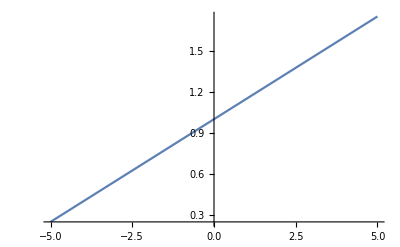

```mathematica
(* Plot diffusivity *)
Plot[(1+k x)/.newConstList,{x,-L/2,L/2}/.newConstList]
```